Se presenta gráficas de los índices de refracción de datos experimentales obtenidos de https://refractiveindex.info/ para diversos materiales

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

```mathematica
Needs["MaTeX`"]
```

### Oro

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en um*)
ℏωAu=h c/λAu; (*eV*)
nau=nau1[[All,2]];
kAu=kau1[[All,2]];
nAu=nau+ I kAu;
```

```mathematica
λAu
```

{187.9,191.6,195.3,199.3,203.3,207.3,211.9,216.4,221.4,226.2,231.3,237.1,242.6,249.,255.1,261.6,268.9,276.1,284.4,292.4,300.9,310.7,320.4,331.5,342.5,354.2,367.9,381.5,397.4,413.3,430.5,450.9,471.4,495.9,520.9,548.6,582.1,616.8,659.5,704.5,756.,821.1,892.,984.,1088.,1216.,1393.,1610.,1937.}

```mathematica
ℏωAu
```

{6.60298,6.47547,6.35279,6.22529,6.10281,5.98505,5.85512,5.73337,5.60389,5.48497,5.36403,5.23281,5.11418,4.98273,4.86358,4.74274,4.61398,4.49366,4.36252,4.24316,4.1233,3.99324,3.87235,3.74269,3.62248,3.50282,3.37238,3.25216,3.12204,3.00194,2.882,2.75161,2.63195,2.50192,2.38184,2.26158,2.13142,2.01151,1.88127,1.76111,1.64114,1.51102,1.39092,1.26087,1.14035,1.02031,0.890668,0.770621,0.640527}

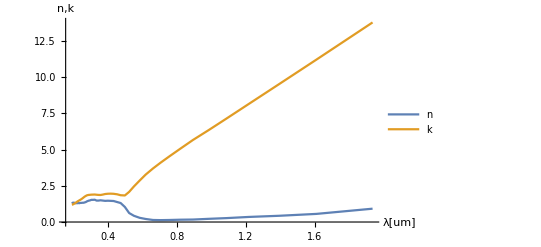

```mathematica
ListLinePlot[{Transpose[{λAu,nau}],Transpose[{λAu,kAu}]},PlotRange->All,AxesLabel->{"λ[um]","n,k"},PlotLegends->{"n","k"}]
```

```mathematica
h c/2.5
```

496.28

```mathematica
upperTicks4=Module[{labels,positions},labels={310,355,414,496,620,827,1240};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

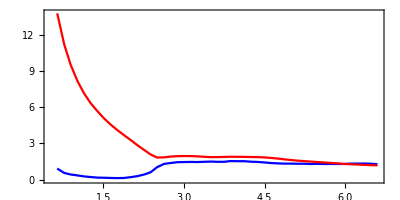

```mathematica
drudeAu=ListLinePlot[{Style[Transpose[{ℏωAu,nau}],Blue],Style[Transpose[{ℏωAu,kAu}],Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["n,k"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.5],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.5]}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["n"],MaTeX["k "]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}],AspectRatio->1/2]
```

```mathematica
Export["drudeAu.svg",drudeAu]
```

drudeAu.svg

### Plata

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
ag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Plata Johnson.csv"];
```

```mathematica
nag1=Drop[Drop[ag,{51,101}],1];
kag1=Drop[ag,{1,52}];
λAg=nag1[[All,1]]*1000;(*λ en um*)
ℏωAg=h c/λAg; (*eV*)
nAg=nag1[[All,2]];
kAg=kag1[[All,2]];
nAgg=nAg+ I kAg;
plata=Transpose[{λAg,nAgg}];
```

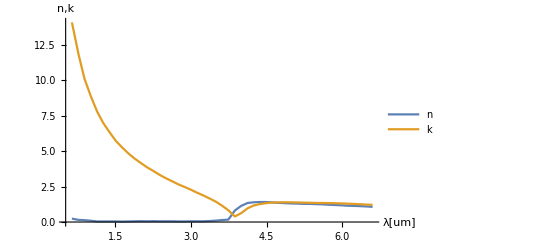

```mathematica
ListLinePlot[{Transpose[{ℏωAg,nAg}],Transpose[{ℏωAg,kAg}]},PlotRange->All,AxesLabel->{"λ[um]","n,k"},PlotLegends->{"n","k"}]
```

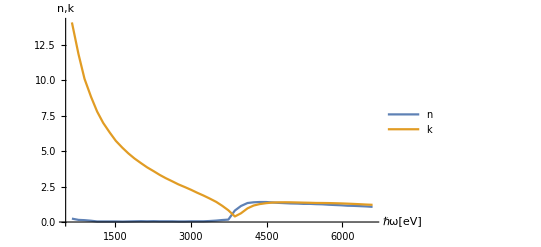

```mathematica
ListLinePlot[{Transpose[{ℏωAg,nAg}],Transpose[{ℏωAg,kAg}]},PlotRange->All,AxesLabel->{"ℏω[eV]","n,k"},PlotLegends->{"n","k"}]
```

### Bismuto

Datos obtenidos de Hagemann  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
bism=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

```mathematica
nbism1=Drop[Drop[bism,{152,303}],1];
kbism1=Drop[bism,{1,153}];
λBism=nbism1[[All,1]];(*λ en um*)
ℏωBism=2 Pi c ℏ/λBism; (*eV*)
nBis=nbism1[[All,2]];
kBis=kbism1[[All,2]];
nBismuto=nBis+ I kBis;
bismuto=Transpose[{λBism,nBismuto}];
```

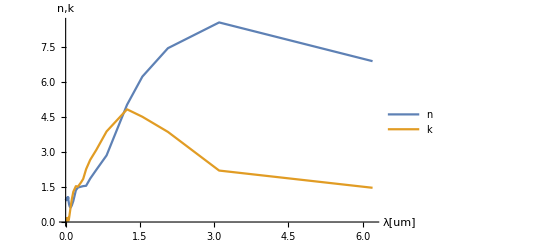

```mathematica
ListLinePlot[{Transpose[{λBism,nBis}],Transpose[{λBism,kBis}]},PlotRange->All,AxesLabel->{"λ[um]","n,k"},PlotLegends->{"n","k"}]
```

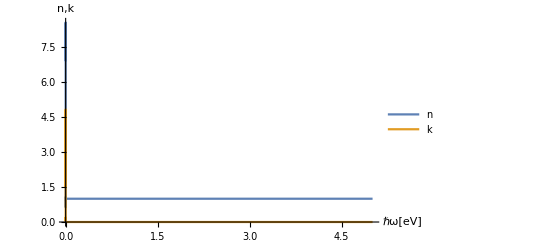

```mathematica
ListLinePlot[{Transpose[{ℏωBism,nBis}],Transpose[{ℏωBism,kBis}]},PlotRange->All,AxesLabel->{"ℏω[eV]","n,k"},PlotLegends->{"n","k"}]
```

```mathematica
bis=ListLinePlot[{Style[Transpose[{ℏωAu,nau}],Blue],Style[Transpose[{ℏωAu,kAu}],Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["n,k"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.5],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.5]}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["n"],MaTeX["k "]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}],AspectRatio->1/2]
```

### Óxido de magnesio

Datos obtenidos de Stephens and Malitson  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
mgO=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Óxido de magnesio Stephens.csv"];
```

```mathematica
mgO1=Drop[mgO,1];
λMgO=mgO1[[All,1]];(*λ en um*)
ℏωMgO=2 Pi c ℏ/λMgO; (*eV*)
nMgO=mgO1[[All,2]];
nmgo=Transpose[{λMgO,nMgO}];
```

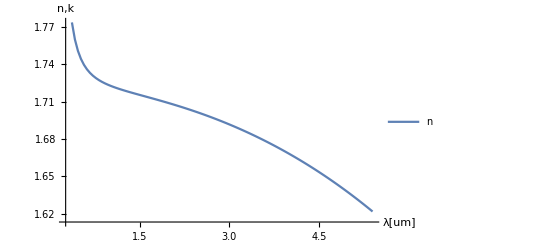

```mathematica
ListLinePlot[{Transpose[{λMgO,nMgO}]},PlotRange->All,AxesLabel->{"λ[um]","n,k"},PlotLegends->{"n"}]
```

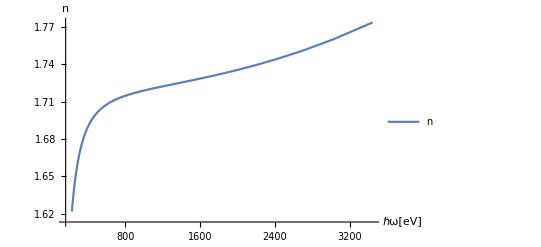

```mathematica
ListLinePlot[{Transpose[{ℏωMgO,nMgO}]},PlotRange->All,AxesLabel->{"ℏω[eV]","n"},PlotLegends->{"n","k"}]
```

### Aluminio

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
alum=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Aluminio Rakic.csv"];
```

```mathematica
alum1=Drop[Drop[alum,{208,415}],1];
λalum=alum1[[All,1]];
ℏωalum=2 Pi c ℏ/λalum; (*eV*)
nalum=alum1[[All,2]];
alum2=Drop[alum,{1,209}];
kalum=alum2[[All,2]];
naluminio=nalum+ I kalum;
```

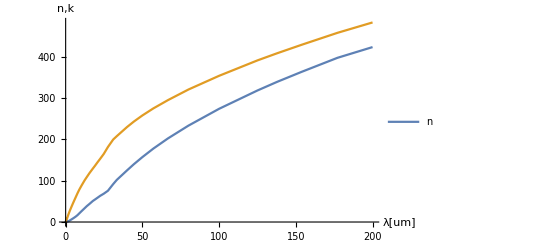

```mathematica
ListLinePlot[{Transpose[{λalum,nalum}],Transpose[{λalum,kalum}]},PlotRange->All,AxesLabel->{"λ[um]","n,k"},PlotLegends->{"n"}]
```

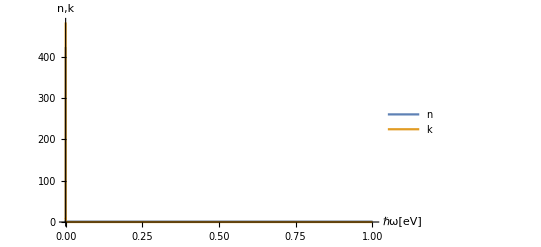

```mathematica
ListLinePlot[{Transpose[{ℏωalum,nalum}],Transpose[{ℏωalum,kalum}]},PlotRange->All,AxesLabel->{"ℏω[eV]","n,k"},PlotLegends->{"n","k"}]
```